# Gaussian Quadrature

```mathematica
(* Import the package Numerical Differential Equation Analysis *)
```

```mathematica
<<  NumericalDifferentialEquationAnalysis`
n = 2;
a = -1;
b = 1;
f[x_]:= (x-1)^3;

list = GaussianQuadratureWeights[n,a,b]

Print["Approximation using Gaussian Quadrature:"]
Sum[list[[i,2]]* f[list[[i,1]]], {i,n}]

Print["Actual:"]
Integrate[f[x], {x,a,b}]
```

{{-0.57735,1.},{0.57735,1.}}

Approximation using Gaussian Quadrature:

-4.

Actual:

-4

## Gram-Schmidt For Polynomials

```mathematica
(* First we create v, a vector containing all of the polynomials up to degree n-1 *)
```

```mathematica
n = 4;
v = Table[x^i, {i,0,n-1}]

(* create basis and u lists which are initialized with the single element v[[1]]*)
basis = u = {v[[1]]};
(* define the projection function *)
proj[u_,v_]:= (∫_-1^1 u*vⅆx)/(∫_-1^1 u*uⅆx)*u;
```

{1,x,x^2,x^3}

```mathematica
(* Each time from i = 2 up to n, subtract the projection of v onto each of the previous vectors to orthogonalize it. *)
```

```mathematica
For[i = 2, i≤ n,i++,
ui = v[[i]] - ∑_(j=1)^(i-1) proj[u[[j]], v[[i]]];
AppendTo[u,ui];
(* e below is the normalized polynomial *)
e = ui/Sqrt[∫_-1^1 ui*uiⅆx];
AppendTo[basis, e];
]
```

```mathematica
basis
```

{1,√(3/2) x,3/2 √(5/2) (-1/3+x^2),5/2 √(7/2) (-(3 x)/5+x^3)}

```mathematica
u
```

{1,x,-1/3+x^2,-(3 x)/5+x^3}

The quadrature points for the n-1th point quadrature are the roots of the n degree orthogonal polynomial:

```mathematica
s = NSolve[u[[4]]==0,x]
```

{{x→-0.774597},{x→0.},{x→0.774597}}

```mathematica
(* Here are the weights and the points See if you can compute the weights yourself by integrating the basis functions. See the book for details. *)
```

```mathematica
GaussianQuadratureWeights[3,-1,1]
```

{{-0.774597,0.555556},{0.,0.888889},{0.774597,0.555556}}

```mathematica
(* Notice that the standard legendre polynomials match our normalized basis polynomials *)
```

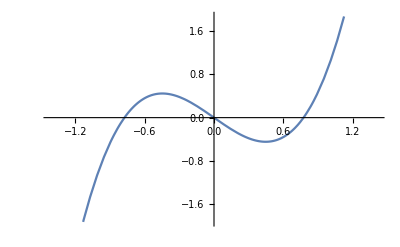

```mathematica
Plot[LegendreP[3,x],{x,-1.4142135623730954,1.4142135623730954}]
```

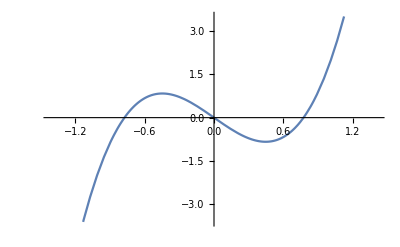

```mathematica
Plot[basis[[4]],{x,-1.4142135623730954,1.4142135623730954}]
```